# 318 Final Project -- Diffusion and Bacteria

## Carter Colton

```mathematica
Clear["'*"];
```

## Part A

Diffusion equation:

```mathematica
D[U,t]=D[D[U,x],x];
```

We want it in polar coordinates:

```mathematica
D[U,t]=Laplacian[U,{r,theta}]=1/r*D[r*D[U,r],r]+1/r^2*D[D[U,theta],theta];
```

Separation of Variables:

```mathematica
T'[t]*R[r]*Θ[θ]=T[t]/r*
```

```mathematica
L=5;
```

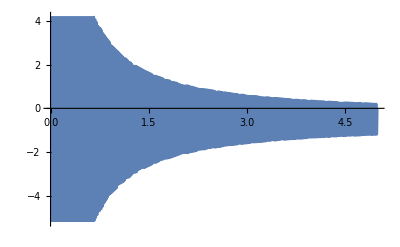

```mathematica
Plot[Sum[Cos[n*Pi/(2*L)*x],{n,1,1000}],{x,0,5}]
```